```mathematica
ClearAll["Global`*"]
```

```mathematica
D2[n_,k_]:=D2[n,k]=If[n<1,0,Sum[D2[Floor[n/j],k-1],{j,2,n}]];D2[n_,0]:=If[n<1,0,1]
DD2[n_,0]:=If[n≥1,1,0]
D22[n_,a_]:=If[n<2^a,0,DD2[n,a]]
D1[n_,z_]:=D1[n,z]=Sum[FactorialPower[z,a]/a! D22[n,a],{a,0,Log[2,n]}];D1[0,z_]:=0
E1[n_,a_,b_]:=E1[n,a,b]=Sum[(-1)^j Binomial[a,j]b^j D1[Floor[n/b^j],a],{j,0,a}]
E2[n_,a_,b_]:=E2[n,a,b]=Sum[(-1)^(a-j) Binomial[a,j]E1[n,j,b],{j,0,a}]
D2E2[n_,k_,b_]:= Sum[ (-1)^j b^j Binomial[k,j] Sum[ Binomial[j,m] D22[n/b^j,k-m],{m,0,j}],{j,0,k}]
lin[n_,b_]:=Sum[(-1)^(k+1)/k E2[n,k,b],{k,1,Log[2,n]}]
lind[n_,b_]:=Sum[(-1)^(k+1)/k D22[n,k],{k,1,Log[2,n]}]
lind2[n_,b_]:=Sum[(-1)^(k+1)/k D2E2[n,k,b],{k,1,Log[2,n]}]
lind2k[n_,b_,k_]:=(-1)^(k+1)/k D2E2[n,k,b]
lindk[n_,b_,k_]:=(-1)^(k+1)/k D22[n,k]
linAdd[n_,b_] := Sum[ b^k/k,{k,1,Log[b,n]}]
linref[n_]:=Sum[ FullSimplify[MangoldtLambda[j]/Log[j]],{j,2,n}]
ldif[n_,b_,k_]:=FullSimplify[Expand[lind2k[n,b,k]]-lindk[n,b,k]]
```

```mathematica
lin[1000,6/3]+linAdd[1000,6/3]
```

445273/2520

```mathematica
lind2[100,-6/3]-(lin[100,6/3]+linAdd[100,6/3])
```

-50/3

```mathematica
Expand[E2[10000,3,2]]
```

-8 D22[1250,0]-24 D22[1250,1]-24 D22[1250,2]-8 D22[1250,3]+12 D22[2500,1]+24 D22[2500,2]+12 D22[2500,3]-6 D22[5000,2]-6 D22[5000,3]+D22[10000,3]

```mathematica
Table[ { n, Expand[E2[10000,n,2]]},{n,1,7}]//TableForm
```

1 | -2 D22[5000,0]-2 D22[5000,1]+D22[10000,1]
2 | 4 D22[2500,0]+8 D22[2500,1]+4 D22[2500,2]-4 D22[5000,1]-4 D22[5000,2]+D22[10000,2]
3 | -8 D22[1250,0]-24 D22[1250,1]-24 D22[1250,2]-8 D22[1250,3]+12 D22[2500,1]+24 D22[2500,2]+12 D22[2500,3]-6 D22[5000,2]-6 D22[5000,3]+D22[10000,3]
4 | 16 D22[625,0]+64 D22[625,1]+96 D22[625,2]+64 D22[625,3]+16 D22[625,4]-32 D22[1250,1]-96 D22[1250,2]-96 D22[1250,3]-32 D22[1250,4]+24 D22[2500,2]+48 D22[2500,3]+24 D22[2500,4]-8 D22[5000,3]-8 D22[5000,4]+D22[10000,4]
5 | -32 D22[312,0]-160 D22[312,1]-320 D22[312,2]-320 D22[312,3]-160 D22[312,4]-32 D22[312,5]+80 D22[625,1]+320 D22[625,2]+480 D22[625,3]+320 D22[625,4]+80 D22[625,5]-80 D22[1250,2]-240 D22[1250,3]-240 D22[1250,4]-80 D22[1250,5]+40 D22[2500,3]+80 D22[2500,4]+40 D22[2500,5]-10 D22[5000,4]-10 D22[5000,5]+D22[10000,5]
6 | 64 D22[156,0]+384 D22[156,1]+960 D22[156,2]+1280 D22[156,3]+960 D22[156,4]+384 D22[156,5]+64 D22[156,6]-192 D22[312,1]-960 D22[312,2]-1920 D22[312,3]-1920 D22[312,4]-960 D22[312,5]-192 D22[312,6]+240 D22[625,2]+960 D22[625,3]+1440 D22[625,4]+960 D22[625,5]+240 D22[625,6]-160 D22[1250,3]-480 D22[1250,4]-480 D22[1250,5]-160 D22[1250,6]+60 D22[2500,4]+120 D22[2500,5]+60 D22[2500,6]-12 D22[5000,5]-12 D22[5000,6]+D22[10000,6]
7 | -128 D22[78,0]-896 D22[78,1]-2688 D22[78,2]-4480 D22[78,3]-4480 D22[78,4]-2688 D22[78,5]-896 D22[78,6]+448 D22[156,1]+2688 D22[156,2]+6720 D22[156,3]+8960 D22[156,4]+6720 D22[156,5]+2688 D22[156,6]+448 D22[156,7]-672 D22[312,2]-3360 D22[312,3]-6720 D22[312,4]-6720 D22[312,5]-3360 D22[312,6]-672 D22[312,7]+560 D22[625,3]+2240 D22[625,4]+3360 D22[625,5]+2240 D22[625,6]+560 D22[625,7]-280 D22[1250,4]-840 D22[1250,5]-840 D22[1250,6]-280 D22[1250,7]+84 D22[2500,5]+168 D22[2500,6]+84 D22[2500,7]-14 D22[5000,6]-14 D22[5000,7]+D22[10000,7]

```mathematica
D2E2[n_,k_,b_]:= Sum[ (-1)^j b^j Binomial[k,j] Sum[ Binomial[j,m] D2[n/b^j,k-m],{m,0,j}],{j,0,k}]
```

```mathematica
D2E2[10,3,3]
```

-26

```mathematica
E2[10,3,3]
```

1

```mathematica
DD2E2[n_,k_,b_]:= Sum[ (-1)^j b^j Binomial[k,j] Sum[ Binomial[j,m] DD2[n/b^j,k-m],{m,0,j}],{j,0,k}]
```

```mathematica
Expand[DD2E2[10000,1,-2]]
```

2 DD2[-5000,0]+2 DD2[-5000,1]+DD2[10000,1]

```mathematica
Expand[DD2E2[10000,1,2]]
```

-2 DD2[5000,0]-2 DD2[5000,1]+DD2[10000,1]

```mathematica
Expand[E2[10,3,3]]
```

1

```mathematica
Table[ {n, D2E2[10,n,3]-E2[10,n,3]},{n,1,20}]//TableForm
```

1 | 0
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 0
17 | 0
18 | 0
19 | 0
20 | 0

```mathematica
linAdd2[n_,b_] := (1/2)Sum[ (b^2)^k/k,{k,1,Log[b^2,n]}]
```

```mathematica
Table[ {n, lin[n,-2]+linAdd2[n,2]-(lin[n,2]+linAdd[n,2])},{n,2,100}]//TableForm
```

2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 0
17 | 0
18 | 0
19 | 0
20 | 0
21 | 0
22 | 0
23 | 0
24 | 0
25 | 0
26 | 0
27 | 0
28 | 0
29 | 0
30 | 0
31 | 0
32 | 0
33 | 0
34 | 0
35 | 0
36 | 0
37 | 0
38 | 0
39 | 0
40 | 0
41 | 0
42 | 0
43 | 0
44 | 0
45 | 0
46 | 0
47 | 0
48 | 0
49 | 0
50 | 0
51 | 0
52 | 0
53 | 0
54 | 0
55 | 0
56 | 0
57 | 0
58 | 0
59 | 0
60 | 0
61 | 0
62 | 0
63 | 0
64 | 0
65 | 0
66 | 0
67 | 0
68 | 0
69 | 0
70 | 0
71 | 0
72 | 0
73 | 0
74 | 0
75 | 0
76 | 0
77 | 0
78 | 0
79 | 0
80 | 0
81 | 0
82 | 0
83 | 0
84 | 0
85 | 0
86 | 0
87 | 0
88 | 0
89 | 0
90 | 0
91 | 0
92 | 0
93 | 0
94 | 0
95 | 0
96 | 0
97 | 0
98 | 0
99 | 0
100 | 0

```mathematica
4/2+16/4+64/6
```

50/3

```mathematica
2/1+4/2+8/3
```

20/3

```mathematica
4/1+16/2+64/3
```

100/3

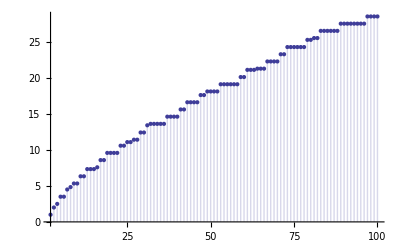

```mathematica
DiscretePlot[lind2[n,-8/3]+linAdd2[n,8/3],{n,2,100}]
```

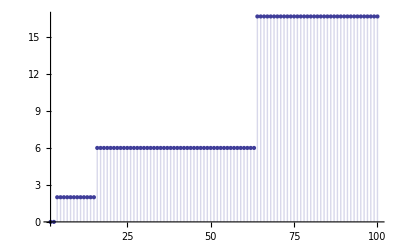

```mathematica
DiscretePlot[linAdd2[n,2],{n,2,100}]
```

```mathematica
2^3^4
```

2417851639229258349412352

```mathematica
2^12
```

4096

```mathematica
(2^3)^4
```

4096

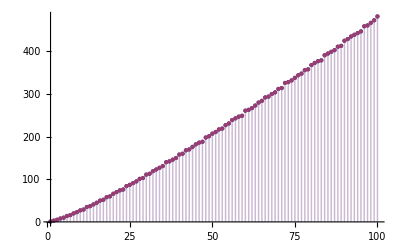

```mathematica
DiscretePlot[ {E1[n,2,-19],D1[n,2]},{n,1,100}]
```

```mathematica
Table[ {E1[n,2,-19],D1[n,2]},{n,1,100}]//TableForm
```

1 | 1
3 | 3
5 | 5
8 | 8
10 | 10
14 | 14
16 | 16
20 | 20
23 | 23
27 | 27
29 | 29
35 | 35
37 | 37
41 | 41
45 | 45
50 | 50
52 | 52
58 | 58
60 | 60
66 | 66
70 | 70
74 | 74
76 | 76
84 | 84
87 | 87
91 | 91
95 | 95
101 | 101
103 | 103
111 | 111
113 | 113
119 | 119
123 | 123
127 | 127
131 | 131
140 | 140
142 | 142
146 | 146
150 | 150
158 | 158
160 | 160
168 | 168
170 | 170
176 | 176
182 | 182
186 | 186
188 | 188
198 | 198
201 | 201
207 | 207
211 | 211
217 | 217
219 | 219
227 | 227
231 | 231
239 | 239
243 | 243
247 | 247
249 | 249
261 | 261
263 | 263
267 | 267
273 | 273
280 | 280
284 | 284
292 | 292
294 | 294
300 | 300
304 | 304
312 | 312
314 | 314
326 | 326
328 | 328
332 | 332
338 | 338
344 | 344
348 | 348
356 | 356
358 | 358
368 | 368
373 | 373
377 | 377
379 | 379
391 | 391
395 | 395
399 | 399
403 | 403
411 | 411
413 | 413
425 | 425
429 | 429
435 | 435
439 | 439
443 | 443
447 | 447
459 | 459
461 | 461
467 | 467
473 | 473
482 | 482

```mathematica
Table[ { n, Expand[E2[10000,n,2]]},{n,1,7}]//TableForm
```

1 | -1
2 | 5
3 | -6
4 | 411
5 | 1139
6 | -794
7 | -1253

```mathematica
lin[10000,2]+linAdd[10000,2]
```

56175529/45045

```mathematica
56175529/45045
```

56175529/45045

```mathematica
linref[100000]
```

991892879/102960

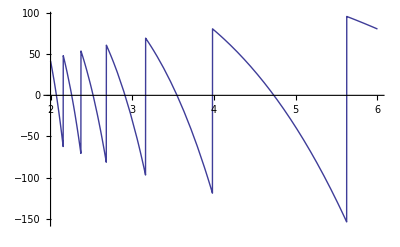

```mathematica
Plot[ lin[1000,n],{n,2,6}]
```

```mathematica
lind2[100,2]
```

-2 (D22[50,0]+D22[50,1])+D22[100,1]+1/2 (-4 (D22[25,0]+2 D22[25,1]+D22[25,2])+4 (D22[50,1]+D22[50,2])-D22[100,2])+1/3 (-8 (D22[25/2,0]+3 D22[25/2,1]+3 D22[25/2,2]+D22[25/2,3])+12 (D22[25,1]+2 D22[25,2]+D22[25,3])-6 (D22[50,2]+D22[50,3])+D22[100,3])+1/4 (-16 (D22[25/4,0]+4 D22[25/4,1]+6 D22[25/4,2]+4 D22[25/4,3]+D22[25/4,4])+32 (D22[25/2,1]+3 D22[25/2,2]+3 D22[25/2,3]+D22[25/2,4])-24 (D22[25,2]+2 D22[25,3]+D22[25,4])+8 (D22[50,3]+D22[50,4])-D22[100,4])+1/5 (-32 (D22[25/8,0]+5 D22[25/8,1]+10 D22[25/8,2]+10 D22[25/8,3]+5 D22[25/8,4]+D22[25/8,5])+80 (D22[25/4,1]+4 D22[25/4,2]+6 D22[25/4,3]+4 D22[25/4,4]+D22[25/4,5])-80 (D22[25/2,2]+3 D22[25/2,3]+3 D22[25/2,4]+D22[25/2,5])+40 (D22[25,3]+2 D22[25,4]+D22[25,5])-10 (D22[50,4]+D22[50,5])+D22[100,5])+1/6 (-64 (D22[25/16,0]+6 D22[25/16,1]+15 D22[25/16,2]+20 D22[25/16,3]+15 D22[25/16,4]+6 D22[25/16,5]+D22[25/16,6])+192 (D22[25/8,1]+5 D22[25/8,2]+10 D22[25/8,3]+10 D22[25/8,4]+5 D22[25/8,5]+D22[25/8,6])-240 (D22[25/4,2]+4 D22[25/4,3]+6 D22[25/4,4]+4 D22[25/4,5]+D22[25/4,6])+160 (D22[25/2,3]+3 D22[25/2,4]+3 D22[25/2,5]+D22[25/2,6])-60 (D22[25,4]+2 D22[25,5]+D22[25,6])+12 (D22[50,5]+D22[50,6])-D22[100,6])

```mathematica
lind[100,2]
```

DD2[100,1]-1/2 DD2[100,2]+1/3 DD2[100,3]-1/4 DD2[100,4]+1/5 DD2[100,5]-1/6 DD2[100,6]

```mathematica
FullSimplify[Expand[Sum[ ldif[100,2,k],{k,1,10}]]]
```

-416/15

```mathematica
Table[{k,ldif[1000,3,k]},{k,1,16}]//TableForm
```

1 | -999
2 | 2526
3 | -3768
4 | 14205/4
5 | -11238/5
6 | 1158
7 | -525
8 | 201/2
9 | -3
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 0

```mathematica
Sum[ ldif[1000,3,k],{k,1,16}]
```

-4137/20

```mathematica
Sum[ 3^k/k,{k,1,Log[3,1000]}]
```

4137/20